# The problem:

Quantum wells are a type of nanostructure obtained by the union of two semiconductor materials with different energy gaps. In particular, one of the materials can be “sandwiched” between two thick layers of the other. The  difference between the gaps causes a confinement effect on the electrons (holes) in the conduction band (valence band) when the length of the well is close to the De Broglie’s wavelength of the electron (hole). Under the right conditions one can confine a single electron (hole) in the well. (To read more about it: https://en.wikipedia.org/wiki/Quantum_well )

-Graphics-
Quantum well. (2022, November 21). In Wikipedia. https://en.wikipedia.org/wiki/Quantum_well

One common combinations of materials used in the fabrication of quantum wells is the junction of GaAs and GaAsAl . As a first approach to the problem we may consider the effective mass and envelope function approximation, that let us write the Schrödinger equation for the electron’s wave function as:
Harrison, P. (2005). Quantum Wells, Wires and Dots. John Wiley &#38; Sons, Ltd. https://doi.org/10.1002/0470010827

-ℏ^2/(2 m^*)(ⅆ^2 Ψ(z))/(ⅆ z^2)+V(z)Ψ(z)=EΨ(z)

Where m^* represents the effective mass of the electron, that for GaAs is m^*=0.067 m_o,  m_o being the electrons mass. V(z) is the confinement potential due to the mismatch between the band gaps in the GaAs/GaAlAs junction; typically it takes values of a few hundred meV. Furthermore, in order to handle the problem more easily and so we won’t have to deal with units, an procedure is needed. The Schrödinger equation can be written as:

ℏ^2/(2 m^*)(ⅆ^2 Ψ(z))/(ⅆ z^2)=(V(z)-E)Ψ(z)

And if we make the following variable changes:

V(z)=Ry^*V̄(z)
E=Ry^*Ē
z=a_0^*z̄

The quantities V̄(z), Ē and z̄ are dimensionless. The units are carried out by the terms Ry^* (effective Rydberg) and a_0^* (effective Bohr radius), which have dimension of energy and length respectively. Thus that give us:

ℏ^2/(2(m^*(a_0^*))^2)(ⅆ^2 Ψ(z))/(ⅆ(z̄)^2)=Ry^*(V̄(z)-Ē)Ψ(z)

If we make the following definitions:

Ry^*=ℏ^2/(2(m^*(a_0^*))^2), a_0^*=100 10^-10 m

Then it is possible to measure all the energies in the problem as effective Rydbergs and all the lengths in effective Bohr radii, which can be chosen to be 100 Ångström.  And we can solve an equation of the form:

-(ⅆ^2 Ψ(z))/(ⅆ(z̄)^2)+V̄(z)Ψ(z)=Ē Ψ(z)

## Parameters:

The parameter d represents the length of the well.

```mathematica
ℏ=1.05457181 10^(−34); (*Js*)
m=9.1093837 10^-31;(*kg*)(*electron's mass*)
meff=0.067*m ; (*effective mass of the electron in GaAs*)
a0=100 10^-10;(*effective Bohr radius 100 Angstroms*)
qe=1.602176634 10^(−19); (*electron's charge*)
Ry=ℏ^2/(2meff a0^2);(*effective Rydberg in Joules*)
RymeV=Ry 1000/qe; (*effective Rydberg in meV*)
d=2; (*length of the well considered in effective Bohr radii*)
zmin=-2d;(*minimum value of z*)
zmax= 2d;(*maximum value of z*)
point=-d/2; (*Commonpoint to check the continuity of the derivative*)
EnergyGuess=0.1;(*parameter to look for the energy*)
V0=100/RymeV;(*value of the potential in effective Rydbergs*)
```

## Solution:

### Potential:

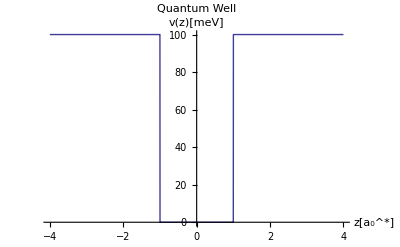

```mathematica
V=Piecewise[{{V0,Abs[z]>d/2},{0,Abs[z]<d/2}}];
Plot[Evaluate[V]RymeV,{z,zmin,zmax},PlotLabel->"Quantum Well",PlotTheme->"Classic",AxesLabel->{"z[a_0^*]","v(z)[meV]"},Exclusions->None]
```

### Methodology:

We need to find two things: the wave function and the energy associated with it. To have a suitable wave function, we need to make sure that the wave function goes to zero in places far away from the inside of the well. And also that the wave function and its derivative are continuous, since that is expected from a well-behaved (no infinite discontinuities) potential. To do that, we need to think about right and left solutions. We will make them go to zero far from the well, and the two functions must meet at some point, and their respective derivatives have to be the same at that point as well.

```mathematica
SetSystemOptions["EvaluateNumericalFunctionArgument"->False];
CommonPoint=Rule[z,point];
leftΨ[Ε_,z]:=First[NDSolve[{-D[Ψ[z],{z,2}]+V Ψ[z]== Ε Ψ[z],Ψ'[zmin]==0.0001,Ψ[zmin]==0},Ψ[z],{z,zmin,z/.CommonPoint}]][[1,2]]
rightΨ[Ε_,z]:=First[NDSolve[{-D[Ψ[z],{z,2}]+V Ψ[z]== Ε Ψ[z],Ψ'[zmax]==0.0001,Ψ[zmax]==0},Ψ[z],{z,z/.CommonPoint,zmax}]][[1,2]]
```

Also, the magnitude of the left function must be equal to the right function at the meeting point.

```mathematica
scalefactorLeft[Ε_]:=leftΨ[Ε,z]/.CommonPoint;
scalefactorRight[Ε_]:=rightΨ[Ε,z]/.CommonPoint;
scaledLeft[Ε_,z]:=leftΨ[Ε,z]scalefactorRight[Ε]/scalefactorLeft[Ε];(*scaledLeft: new left function that should match the right one.*)
```

We also care about the derivative of each solution, right and left.

```mathematica
DRight[Ε_,z]:=D[rightΨ[Ε,z],z];
DLeft[Ε_,z]:=D[scaledLeft[Ε,z],z];
```

The energy that corresponds with an bounded eigenstate should be one that makes the derivative of the wave function continuous. With a parameter when the function will start guessing for the energy of 0.1 Ry^* this function give us the ground state of the problem, equal to 1.59894 Ry^*.

```mathematica
Energy=Ε/.FindRoot[(DLeft[Ε,z]/.CommonPoint)==(DRight[Ε,z]/.CommonPoint),{Ε,EnergyGuess,EnergyGuess+EnergyGuess/10.0}]
```

1.59894

With the energy we can calculate the actual wave function simply replacing that energy found in the Schrödinger equation

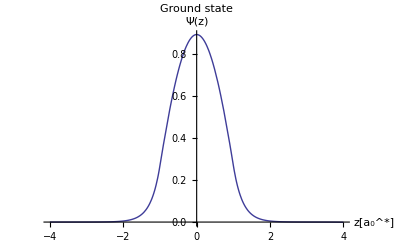

```mathematica
result=First[Ψ[z]/.NDSolve[{-D[Ψ[z],{z,2}]+V Ψ[z]== Energy Ψ[z],Ψ'[zmin]==0.0001,Ψ[zmin]==0},Ψ[z],{z,zmin,zmax}]];
ConstNorm=1/√NIntegrate[result^2,{z,zmin,zmax}];(*normalization constant*)
Plot[ConstNorm result,{z,zmin,zmax},PlotRange->All,PlotLabel->"Ground state",PlotTheme->"Classic",AxesLabel->{"z[a_0^*]","Ψ(z)"}]
```

We can find all the energies just by making and educated guess with the “EnergyGuess” parameter. In the next function we use the values of {0.1 Ry^*, 6 Ry^*, 9 Ry^*}  to find the energies in the well and use that as an input to find the rest of the wave functions confined in the well. As a note, we could keep on finding energies and wave functions, but at some point we would hit the top of the well and that wouldn’t give us well behaved solutions (that decay exponentially as they go to high and low values of z).

```mathematica
UnnormWaveFuncts=Table[ First[Ψ[z]/.NDSolve[{-D[Ψ[z],{z,2}]+V Ψ[z]== ener Ψ[z],Ψ'[zmin]==0.0001,Ψ[zmin]==0},Ψ[z],{z,zmin,zmax}]],{ener,Table[Ε/.FindRoot[(DLeft[Ε,z]/.CommonPoint)==(DRight[Ε,z]/.CommonPoint),{Ε,eng,eng+eng/10.0}],{eng,{0.1,6,9}}]}];
NormConsts=Table[1/√NIntegrate[UnnormWaveFuncts[[i]]^2,{z,zmin,zmax}],{i,1,3}];
```

```mathematica
NormWaveFuncts=UnnormWaveFuncts NormConsts;
```

Once the wave functions are normalized we can plot them in the quantum well. As a help in visualization, each wave function is offset upwards by each corresponding energy level. And, also, the wave functions are multiplied by a factor of 10, to compensate for the scale.

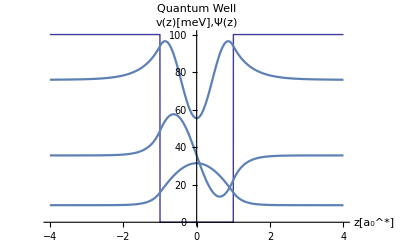

```mathematica
PotentialPlot=Plot[Evaluate[V]RymeV,{z,zmin,zmax},PlotLabel->"Quantum Well",PlotTheme->"Classic",AxesLabel->{"z[a_0^*]","v(z)[meV],Ψ(z)"},Exclusions->None];
EnergiesInMev=RymeV*Table[Ε/.FindRoot[(DLeft[Ε,z]/.CommonPoint)==(DRight[Ε,z]/.CommonPoint),{Ε,eng,eng+eng/10.0}],{eng,{0.1,6,9}}];
PlotsWavesFun=Table[Plot[25NormWaveFuncts[[i]]+EnergiesInMev[[i]],{z,zmin,zmax},PlotRange->All],{i,1,3}];
Show[PotentialPlot,PlotsWavesFun]
```

This is basically the same result obtained by the author of the book  Quantum Wells, Wires and Dots, Harrison, by other methods.

-Graphics-;

Harrison, P. (2005). Quantum Wells, Wires and Dots. John Wiley &#38; Sons, Ltd. https://doi.org/10.1002/0470010827